# Molecular Dynamics Notes

## Enter subtitle here

Enter subsubtitle here

Phil Shea

Enter department here

```mathematica
DateString[]
```

Wed 11 Dec 2024 19:12:25

Enter date here

## General Parameters

### Layout of the Initial Positions

#### Area of Veroni Cell

The initial position is based on a hexagonal grid oriented to the box sides.  Let b_x and b_y be half the sides of the box; the box has corners {{-b_x,-b_y},{b_x,-b_y}, {b_x,b_y},{-b_x, b_y}}   The box area is then the product of these, and the density is ρ = N / (4 b_xb_y), where N is the number of particles in the system.  In the figure below, Q_1 is the center particle, and positions H, I, J, K, L, and M are the adjacent particles.  Let the hexagonal lattice have particle spacing a (Q_1 - J below). The Veroni cell around each particle consists of twelve 30-60-90 right triangles with sides a/2 (Q_1-S_1 in the figure below), a/(2√3) (S_1-E), and hypotenuse a/√3 (Q_1 - E; the ‘ marks are from the GeoGebra drawing program indicating how many time the point was used in the drawing).

-Graphics-

See Fukshansky 2011

The hypotenuse (Q_1 - E) is given by the following:

```mathematica
Solve[a/2 ==r Cos[30 Degree],r]
```

{{r→a/(√3)}}

The short side is therefore

```mathematica
(a/√3)Sin[30 Degree]
```

a/(2 √3)

The area occupied by one particle is then:

```mathematica
area=12(a/2)(a/(2 √3))(1/2)
```

(√3 a^2)/2

To achieve a specified density, solve the following:

```mathematica
Solve[(√3 a^2)/2==1/ρ,a]
```

{{a→-(√2)/(3^(1/4) √ρ)},{a→(√2)/(3^(1/4) √ρ)}}

The paper from 1980 claimed a density of ρ = 1/π and an a of about 1.9σ

```mathematica
α79=Simplify[(√2)/(3^(1/4) √(1/π))]
```

(√(2 π))/3^(1/4)

```mathematica
a79=N[α79]
```

1.90463

The box dimensions can be decided for a desired density.  ρ = N/(4 b_x b_y) = N/(2√3b_x^2) (where b_y = √3 b_x/2

```mathematica
Bx[K_,ρ_]=√(K/(2 √3 ρ))
```

(√(K/ρ))/(√2 3^(1/4))

```mathematica
Bx[256, 1/π]
```

(8 √(2 π))/3^(1/4)

The particle positions then will be Nr rows each having Nc particles (this assumes N is composite).  The following function will place a row of n particles spaced by a starting at position {x, y}:

```mathematica
ClearAll[ placeR];
placeR::usage="placeR[n, a, x, y] will place a row of n particles spaced by a starting 
at position {x, y}"
placeR[n_, a_, x_, y_]:=Table[{x + i a, y},{i,0,n-1}]
```

Here is an example:

```mathematica
placeR[4, .3, .3/4, 0]
```

{{0.075,0},{0.375,0},{0.675,0},{0.975,0}}

This function will fill a rectangle, and the two parameter version will make the standard rectangle.

```mathematica
ClearAll[ fill];
fill::usage="fill[ Bx, By, K] will place K particles in a hexagonal grid in a rectangle of 
size 2Bx x 2By.  If N is not a perfect square such that all the rows have the same number of 
particles, it may be adjusted to fit the dimensions. Returns a two element list {parms, pnts}; parms is a list {ρ, a, Nc, Nr,Bx,By} 
repectivley the density, the particle spacing, the number of rows and columns, and the
input box parmaeters.  pnts is a list of {x, y} coordinates of the K particle positions.

fill[ Bx, K] (the two parameter version) will set By to the default of (√3/2)Bx.";
fill[Bx_, By_, K_]:= Module[{ρ=K/(4 Bx By), a, Nc, Nr, r, c}, 
	a=√(2/(ρ √3)); c=√3/2; Nc=Round[2 Bx/a]; Nr=Round[K/Nc];
	{{ρ, a, Nr, Nc, Bx, By},
	Table[placeR[Nc, a, (a/4)(1+2Mod[i,2])-Bx,a c(i+1/2)-By],{i,0,Nr-1}]}];
	fill[Bx_, K_]:= fill[Bx, (√3/2)Bx,K]
```

Here is an example of 10 particles:

```mathematica
pnts=fill[10,25]
```

{{1/(8 √3),4,5,5,10,5 √3},{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}}

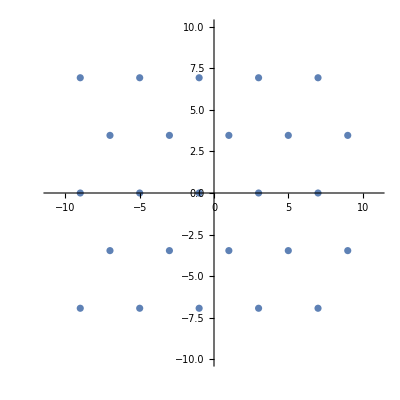

```mathematica
ListPlot[Flatten[pnts⟦2⟧,1],AspectRatio->1, PlotRange-> {{-11,11},{-10,10}},GridLines->{{-10,10},{-10√3/2,10√3/2}}]
```

A function to plot the points returned by fill[] will be useful:

```mathematica
ClearAll[plotPnts];
 plotPnts[pnts_]:=Module[{Bx=pnts⟦1,5⟧, By=pnts⟦1,6⟧, box},box={{-Bx, Bx}, {-By, By}};
 ListPlot[Flatten[pnts⟦2⟧, 1], AspectRatio->1, PlotRange->1.1box, GridLines->box]]
```

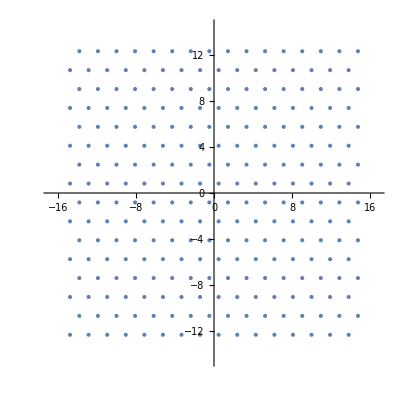

```mathematica
pnts256=fill[Bx[256, 1/π],256];
p256=plotPnts[pnts256]
```

Here is 256 particle array, with a focus on particle 189.  The red circle is the skin range of 3.5, and the green circle is the correlation range of 5.  The magenta circled particle is the next nearest particle on the row, and the blue circled particle is the second next nearest particle, just inside the skin.

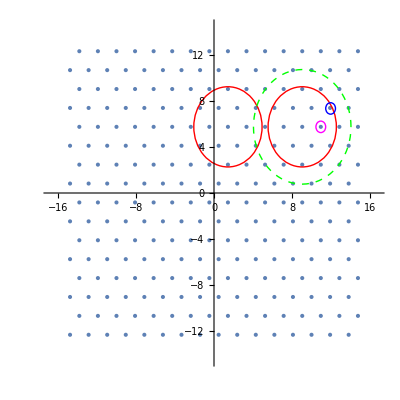

```mathematica
p1=Flatten[pnts256⟦2⟧,1]⟦189⟧;
p2=Flatten[pnts256⟦2⟧,1]⟦190⟧;
p3=Flatten[pnts256⟦2⟧,1]⟦207⟧;
p4=Flatten[pnts256⟦2⟧,1]⟦189-4⟧;
Show[p256,Graphics[{Red,Circle[p1,3.5]}],Graphics[{Red,Circle[p4,3.5]}],Graphics[ {Magenta,Circle[p2,0.5]}],Graphics[{Green, Dashed,Circle[p1, 5]}],Graphics[ {Blue, Circle[p3,0.5]}]]
```

The red circles above show that they do not overlap. They could be set to 2a so that they would touch. There would be a few more interacting particles then, and at initialization, six particles would be sitting on the skin.

```mathematica
Simplify[p2-p1]
```

{(√(2 π))/3^(1/4),0}

```mathematica
Simplify[EuclideanDistance[p1,p2]]
```

(√(2 π))/3^(1/4)

```mathematica
nnnd=Simplify[EuclideanDistance[p1,p3]/α79] (*next nearest neighbor distance in 1/π density units*)
```

√3

```mathematica
N[%]
```

3.29891

The third nearest neighbor is 2a, which is just outside the skin.

```mathematica
tnnnd=2α79
```

(2 √(2 π))/3^(1/4)

```mathematica
N[%]
```

3.80925

### Angular Momentum

When applying random velocities to the particles, the velocities in the x and y directions will each be drawn from a zero-mean Gaussian distribution. The sum of velocities in the x and y direction will therefore also be zero-mean, but will have a substantial variance: for N particles, the variance will be Nσ^2.  Therefore, after initialization, we need to measure the momentum in the x and y directions and subtract that average per-particle momentum from each particle.

The same is true for angular momentum. It just won’t do for the whole system to be rotating, even a little. It is easy to measure the angular momentum. For a particle with a vector position x and vector velocity v, and particle mass m, the angular momentum about the origin is L = x × m v. In two dimensions,

```mathematica
A ={ax,ay,az};V ={vx,vy,vz};L=Cross[A,V]
```

{-az vy+ay vz,az vx-ax vz,-ay vx+ax vy}

This is very simple when the z components are zero.

```mathematica
L/.{az-> 0, vz->0}
```

{0,0,-ay vx+ax vy}

The total angular momentum is then L =∑_(i=1)^N x_i×v_i, where we assume m = 1. This can also be considered as an average rotation rate Ω, and the angular momentum can then also be expressed as L =∑_(i=1)^N r_iω =ω∑_(i=1)^N r_i, where r_i is the radial component of the particle i in cylindrical coordinates (that is, its distance from the origin). If S = ∑_(i=1)^N r_i, then the average rotation rate is given by ω = L/S, and therefore the ith particle’s share of the rotation is l_i = ω r_i.

We can calculate ω, and then say that l = ax vy - ay vx. This is insufficient to calculate a velocity vector, but the velocity vector is orthogonal to the particle vector, so their dot product will be zero.

```mathematica
Solve[l==ax vy-ay vx&&ax vx+ay vy==0,{vx,vy}]
```

{{vx→-(ay l)/(ax^2+ay^2),vy→(ax l)/(ax^2+ay^2)}}

#### Numerical Assessments

The value of S is large:

```mathematica
S=Apply[Plus,Map[Norm,N[Flatten[pnts256⟦2⟧,1]]]]
```

2786.81

One measurement of L was around 58. ω is then

```mathematica
58/S
```

0.0208123

```mathematica
%/(2π)
```

0.00331239

```mathematica
1/%
```

301.897

So, with that high value of L, it would take a time of almost 302, or 30,000 time steps to make a full rotation. However, only a small rotation would be a problem with the crystal interfaces at the boundaries.

The maximum range is a bit over 19:

```mathematica
Max[Map[Norm,N[Flatten[pnts256⟦2⟧,1]]]]
```

19.2593

This means that even the farthest particles will only get less than 1% of the total angular momentum, but this is still more than twice what they would get if the momentum was evenly divided among the 256 particles.

```mathematica
S/%
```

144.699

## Initialization

For the following, see Reif, pg. 249, eq. 7.5.7. The mean kinetic energy of a a particle in any dimension is (1/2)kT, where k is in units of temperature per unit of energy, and T is the temperature in units defined by k. The energy of a particle of mass m = 1 is 1/2v^2 which can be broken into x and y components (⟨E⟩ = 1/2 v_x^2+1/2 v_y^2=k T , so that defining k = 1, each component has an expected velocity squared of T.

```mathematica
ClearAll[ngt];
ngt[n_,T_]=GammaDistribution[n,2 T];
{Mean[ngt[n,T]],Variance[ngt[n,T]]}
```

{2 n T,4 n T^2}

```mathematica
ngt1=ngt[256,0.015];
ngtpdf1=PDF[ngt1,x]
```

Piecewise[{{2.14686×10^-115 ⅇ^(-33.3333 x) x^255, x>0}, {0, True}}]

```mathematica
{Mean[ngt1],Variance[ngt1]}
```

{7.68,0.2304}

```mathematica
7.68/256/2
```

0.015

```mathematica
Apply[Plus,Map[#^2&,RandomVariate[NormalDistribution[0,√0.015 ],2 10]]]
```

0.256092

```mathematica
ClearAll[ns];
ns[n_,T_]:=Apply[Plus,Map[#^2&,RandomVariate[NormalDistribution[0,√T],2n]]]
```

```mathematica
n0=256;T0=0.015;ns[n0,T0]
```

7.15937

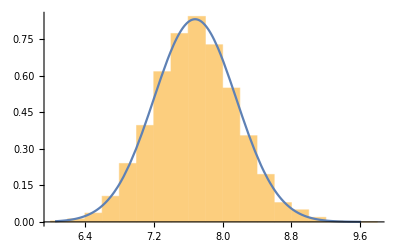

```mathematica
data=Table[ns[n0,T0],10000];
Show[Histogram[data,20,"PDF"],Plot[PDF[NormalDistribution[2n0 T0,2 √n0 T0],x],{x,Min[data],Max[data]}]]
```

```mathematica
Through[{Mean,Variance}[data/(2*256)]]
```

{0.0150021,8.92465×10^-7}

```mathematica
√(%⟦2⟧)/%⟦1⟧
```

0.0629714

So around the melting temperature, there is a 6% standard deviation when generating data.

```mathematica
ClearAll[data];Share[]
```

8647880

#### Test Data

Here is some data used to test the Julia MD2 routines.

```mathematica
N[fill[9,9]]
```

{{0.032075,6.,3.,3.,9.,7.79423},{{{-7.5,-5.19615},{-1.5,-5.19615},{4.5,-5.19615}},{{-4.5,0.},{1.5,0.},{7.5,0.}},{{-7.5,5.19615},{-1.5,5.19615},{4.5,5.19615}}}}

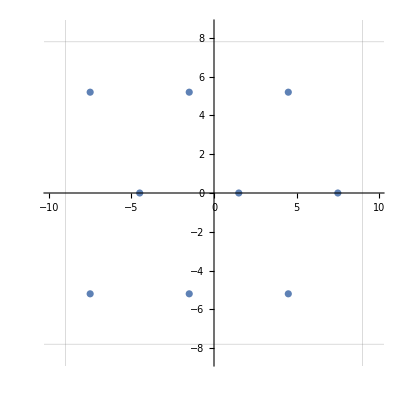

```mathematica
plotPnts[%]
```

#### Potentials 1/r^n

The standard repulsive potential is given by:

```mathematica
ClearAll[rn];
rn[r_, n_]:= 1/r^n
```

Here is the form for a particular n:

```mathematica
rn[r,5]
```

1/r^5

And here are some interesting values of that.

```mathematica
test={1/2, 1, 2,a79, 3, 3.4999, 7/2, 4, nnnd, tnnnd};
(* The explicit rationals are good test values whose results are easily done in your head (except for 7/2, which is the skin distance). a79 is the 1/pi density. 3.4999 is just inside the 3.5 skin value.*)
Map[ rn[#,5]&,test]
```

{32,1,1/32,0.0398981,1/243,0.00190424,32/16807,1/1024,1/(12 √2 3^(1/4) π^(5/2)),0.00124681}

The force is the derivative with respect to r:

```mathematica
f[r_]=D[rn[r,5],r]
```

-5/r^6

Here are the resulting forces at those same interesting values.

```mathematica
Map[f,test]
```

{-320,-5,-5/64,-0.10474,-5/729,-0.00272042,-320/117649,-5/4096,-5/(24 √3 π^3),-0.00163656}

The skin at 3.5σ yields the following ratios to the mean separation in a hexagonal grid:

```mathematica
{rn[3.5,5]/rn[a79,5],f[3.5]/f[a79]}
```

{0.0477208,0.0259687}

The number of particles expected in a circular region of radius r is ρ π r^2, but with the density ρ = 1/π, the expected number of particles is simply r^2

```mathematica
Block[{ρ=1/π},ρ π{3.5^2,5^2}]
```

{12.25,25}

The minimum potential energy of the system on a per particle basis is the energy of six particles at a, and six more at nnnd = √3 a. Therefore the minimum potential energy per particle is half the sum of all twelve (since we ascribe half the potential energy to each pair).

```mathematica
pe=(6rn[a79,5]+6rn[nnnd,5])/2
```

0.312144

#### Setting the Potential to Zero at r_skin

The potential has a step in it:

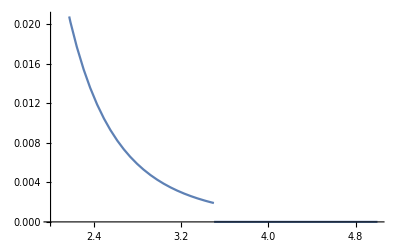

```mathematica
Plot[Piecewise[{{rn[x,5],x<3.5},{0,True}}],{x, 2, 5}]
```

However, the MD2 code has never really dealt with the step, in that the velocity of a particle crossing the step was never diminished in the direction it crossed. In effect, the step was not there, but the potential energy calculation reported it.  If rn[] was defined with the step subtracted, the force would be unchanged, but the potential would be a little lower. The step height is at r = 7/2, so the excess P.E. per particle is given by:

```mathematica
step=N[6rn[7/2,5]/2]
```

0.00571191

If we were to subtract that from the P.E. function rn[] the per particle P.E would be lower by (in percent):

```mathematica
100step/pe
```

1.82989

We can find the nearest points in the following way. Note that when the points are left in symbolic form, the distance returned is the square for some unknown reason. Applying N[] to the list and the point yields the desired results.

```mathematica
Nearest[Flatten[N[pnts256⟦2⟧],1]-> All,N[p2],{All,3.5}]
```

{<|Element→{10.9516,5.77309},Index→190,Distance→0.|>,<|Element→{9.99928,7.42254},Index→206,Distance→1.90463|>,<|Element→{11.9039,7.42254},Index→207,Distance→1.90463|>,<|Element→{12.8562,5.77309},Index→191,Distance→1.90463|>,<|Element→{9.99928,4.12364},Index→174,Distance→1.90463|>,<|Element→{9.04697,5.77309},Index→189,Distance→1.90463|>,<|Element→{11.9039,4.12364},Index→175,Distance→1.90463|>,<|Element→{10.9516,9.072},Index→222,Distance→3.29891|>,<|Element→{8.09466,7.42254},Index→205,Distance→3.29891|>,<|Element→{13.8085,7.42254},Index→208,Distance→3.29891|>,<|Element→{8.09466,4.12364},Index→173,Distance→3.29891|>,<|Element→{13.8085,4.12364},Index→176,Distance→3.29891|>,<|Element→{10.9516,2.47418},Index→158,Distance→3.29891|>}

Rather than work with a list of associations, we can simply ask for the distances:

```mathematica
skinlst = Nearest[Flatten[N[pnts256⟦2⟧],1]-> "Distance",N[p2],{All,3.5}]
```

{0.,1.90463,1.90463,1.90463,1.90463,1.90463,1.90463,3.29891,3.29891,3.29891,3.29891,3.29891,3.29891}

These can be handed to rn[] to compute the PEs as a list :

```mathematica
rn[skinlst⟦2;;⟧,5]/2
```

{0.019949,0.019949,0.019949,0.019949,0.019949,0.019949,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973}

Summing is easy:

```mathematica
pe12=Apply[Plus,%]
```

0.127373

### Distribution of Regressions of Uncorrelated Data

The difficulty of deciding when the temperature profiles are truly uncorrelated requires we examine the distribution of the slope estimate.

```mathematica
βe = (∑_(i=1)^n Subscript[x, i] Subscript[y, i]-n x̄ ȳ)/((n-1)Sx)
```

(-n x̄ ȳ+∑_(i=1)^n x_i y_i)/((-1+n) Sx)

```mathematica
βe2=βe//.{Subscript[x, i]-> i,Sx->√((n^2+2)/12),x̄-> (n+1)/2, ȳ-> 1/n∑_(i=1)^n Subscript[y, i]}
```

(2 √3 (-1/2 (1+n) ∑_(i=1)^n y_i+∑_(i=1)^n i y_i))/((-1+n) √(2+n^2))

We can combine the two sums:

```mathematica
βe3=(2 √3 ∑_(i=1)^n ((i-(n+1)/2) Subscript[y, i]))/((-1+n) √(2+n^2))
```

(2 √3 ∑_(i=1)^n (i+1/2 (-1-n)) y_i)/((-1+n) √(2+n^2))

```mathematica
FullSimplify[∑_(i=1)^n (i-(n+1)/2) ]
```

0

```mathematica
FullSimplify[∑_(i=1)^n (i-(n+1)/2)^2 ]
```

1/12 n (-1+n^2)

```mathematica
n2[n_]=FullSimplify[((2 √3)/((-1+n) √(2+n^2)))^2 1/12 n (-1+n^2),Assumptions->n>3]
```

(n (1+n))/((-1+n) (2+n^2))

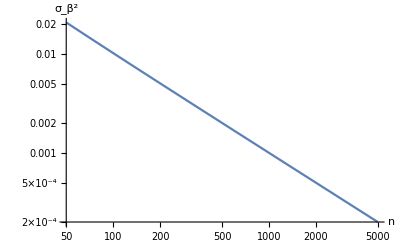

```mathematica
LogLogPlot[n2[n],{n,50,5000},PlotRange->Full,GridLines->Automatic,AxesLabel-> {"n", Subscript[σ, β]^2}]
```

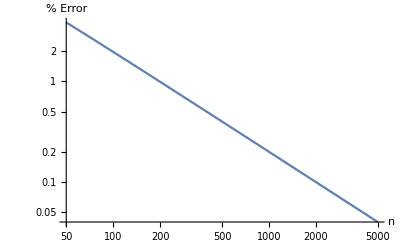

```mathematica
LogLogPlot[100(Abs[(1/n)-n2[n]])/n2[n],{n,50,5000},PlotRange->Full,GridLines->Automatic,AxesLabel-> {"n","% Error"}]
```

```mathematica
Factor[2n^3+6n^2+2n]
```

2 n (1+3 n+n^2)

```mathematica
Apart[12 n (1+3 n+n^2)/(6(n-1)^2(n^2+2))]
```

10/(3 (-1+n)^2)+40/(9 (-1+n))-(2 (-10+11 n))/(9 (2+n^2))

## Application of the Virial Theorem

The Virial Theorem for r^-n potentials states that the total kinetic energy is related to the total potential energy as 2⟨K_T⟩=-n⟨U_T⟩, where the angle brackets denote averages. Combine this with the pressure equation P = ρ⟨Subscript[K, T]⟩(1+(n⟨U_T⟩)/(2⟨K_T⟩)), where ρ is the density, the pressure becomes simply 2ρ⟨K_T⟩

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}